## Penrose’s Echos from Five Dimensions

#### Rotation Matrix and Eigen Vectors

```mathematica
rotationMatrix = RotateLeft[IdentityMatrix[5]];
rotationMatrix//TraditionalForm
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0)

The eigen vectors of this rotation matrix provide the appropriate 2D-3D split for the projection

```mathematica
eigenVectors = Eigenvectors[rotationMatrix];
```

#### Projection Plane

Span vectors

```mathematica
u=Normalize[Re[eigenVectors[[1]]]]//FullSimplify;
v = Normalize[Im[eigenVectors[[1]]]] //FullSimplify;
```

Projector

```mathematica
p={u,v};
p//MatrixForm
```

(-1/2 √(3/5+1/(√5)) | (-1+√5)/(2 √10) | (-1+√5)/(2 √10) | -1/2 √(3/5+1/(√5)) | √(2/5)
1/2 √(1-1/(√5)) | -1/2 √(1+1/(√5)) | 1/2 √(1+1/(√5)) | -1/2 √(1-1/(√5)) | 0)

#### Orthogonal Space

Span vectors and projector

```mathematica
y={Normalize[Re[eigenVectors[[4]]]],Normalize[Im[eigenVectors[[4]]]],Normalize[{1,1,1,1,1}]}//FullSimplify;
y//MatrixForm
```

((-1+√5)/(2 √10) | -1/2 √(3/5+1/(√5)) | -1/2 √(3/5+1/(√5)) | (-1+√5)/(2 √10) | √(2/5)
1/2 √(1+1/(√5)) | 1/2 √(1-1/(√5)) | -1/2 √(1-1/(√5)) | -1/2 √(1+1/(√5)) | 0
1/(√5) | 1/(√5) | 1/(√5) | 1/(√5) | 1/(√5))

#### The Convex Hull

Lattice points, whose orthogonal projection lies inside the convex hull are the close by lattice points

```mathematica
voronoiCell = Tuples[{0,0.999},5];
convexHullSeed = N[y].#&/@voronoiCell;
```

```mathematica
convexHull =ConvexHullMesh[convexHullSeed];
convexHullRegion = ConvexHullRegion[convexHullSeed];
vertices = convexHullRegion[[1]];
faces =vertices[[#]]&/@convexHullRegion[[2]];
```

```mathematica
GraphicsRow[{Graphics3D[Ball[#,0.1]&/@convexHullSeed],convexHull,Graphics3D[{Opacity[0.5],Polygon[#]&/@faces,Ball[#,0.1]&/@convexHullSeed}]}]
```

-Graphics-

#### The lattice

```mathematica
Subscript[ℤ, 5]=N[Tuples[Range[-5,5],5]];
Subscript[ℤ, 5]//Length
```

161051

```mathematica
Subscript[ℤ, 5] = (#+{0.2,0.2,0.2,0.2,-0.8})&/@Subscript[ℤ, 5];
```

Select points that are projected into the convex hull

```mathematica
selPoints = Select[Subscript[ℤ, 5],RegionMember[convexHull,Chop[{y[[1]].#,y[[2]].#,y[[3]].#}]]&];
Length[selPoints]
```

673

#### Construct the tiling

```mathematica
spans = Subsets[{1,2,3,4,5},{2}];
e=IdentityMatrix[5];
eps = 10^-6;
polygonDataFunction[point_,dir_]:={point,point+UnitVector[5,dir[[1]]],point+UnitVector[5,dir[[1]]]+UnitVector[5,dir[[2]]],point+UnitVector[5,dir[[2]]]}
NMemberQ[set_,point_]:=Or@@(#<eps&/@(Total[Abs[N[#-point]]]&/@set))
```

```mathematica
polygonBasePoints =Function[dir,Select[selPoints,And@@(NMemberQ[selPoints,#]&/@(polygonDataFunction[#,dir]&@#))&]]/@spans;
polygonData=MapThread[Function[point,polygonDataFunction[point,#2]]/@#1&,{polygonBasePoints,spans}];
projectedPolygonData = Map[Chop@({u.#,v.#})&,polygonData,{3}];
```

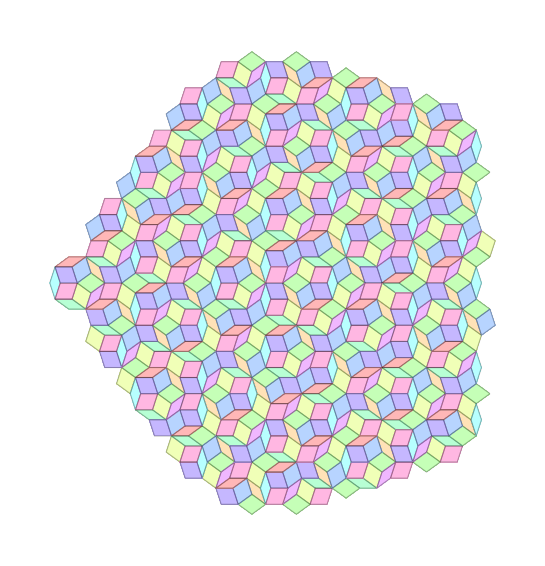

```mathematica
colors = Lighter[Hue[#/10]&/@Range[10],.6];
Graphics[{Opacity[0.7],EdgeForm[Directive[Opacity[0.3],Black]],MapThread[{#1,Function[poly,poly//Polygon]/@#2}&,{colors,projectedPolygonData}]}]
```